```mathematica
Needs["NonlinearRegression`"]
```

ConfidenceLevel::shdw: Symbol "ConfidenceLevel" appears in multiple contexts {"HypothesisTesting`", "Global`"}; definitions in context "HypothesisTesting`" may shadow or be shadowed by other definitions.

NonlinearRegress::shdw: Symbol "NonlinearRegress" appears in multiple contexts {"NonlinearRegression`", "Global`"}; definitions in context "NonlinearRegression`" may shadow or be shadowed by other definitions.

```mathematica
A=Transpose[{{3.775,5.010,6.631,7.917,8.823,5.816,9.562,14.920,4.488,12.437,16.446,22.362,34.743},{0.41,1.48,2.5,3.26,3.70,2.04,3.91,5.29,1.104,4.85,5.6,6.06,6.37}}]
```

{{3.775,0.41},{5.01,1.48},{6.631,2.5},{7.917,3.26},{8.823,3.7},{5.816,2.04},{9.562,3.91},{14.92,5.29},{4.488,1.104},{12.437,4.85},{16.446,5.6},{22.362,6.06},{34.743,6.37}}

```mathematica
Export["C:\\IRE02.dat",Transpose[Join[Transpose[A],{Table[0.05,{i,Length[A]}]}]]]
```

C:\IRE02.dat

```mathematica
Export["C:\\IRE02b.dat",Transpose[Join[Transpose[A],{Table[0.05,{i,Length[A]}],Table[0.05,{i,Length[A]}]}]]]
```

C:\IRE02b.dat

```mathematica
"C:\\IRE02b.dat"
```

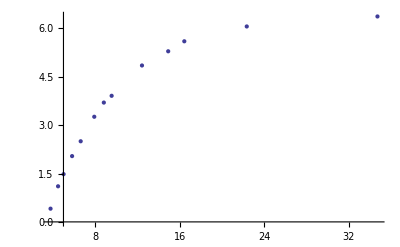

```mathematica
AP=ListPlot[A]
```

```mathematica
NonlinearRegress[A,m(1-2 Exp[-x/t]),{m,t},x,ConfidenceLevel ->.95]
```

{BestFitParameters→{m→6.10565,t→5.27542},ParameterCITable→ | Estimate | Asymptotic SE | CI
m | 6.10565 | 0.0928267 | {5.90134,6.30996}
t | 5.27542 | 0.0936383 | {5.06933,5.48152},EstimatedVariance→0.030266,ANOVATable→ | DF | SumOfSq | MeanSq
Model | 2 | 213.429 | 106.714
Error | 11 | 0.332926 | 0.030266
Uncorrected Total | 13 | 213.762 | 
Corrected Total | 12 | 46.905 | ,AsymptoticCorrelationMatrix→(1. | 0.621684
0.621684 | 1.),FitCurvatureTable→ | Curvature
Max Intrinsic | 0.00975343
Max Parameter-Effects | 0.0306833
95. % Confidence Region | 0.50111}

```mathematica
(5.901341457941188+6.30996163835896)/2
```

6.10565

```mathematica
FFA=FindFit[A,{m(1-2 Exp[-x/t]),{0≤m<=10,0≤t≤50}},{m,t},x]
```

FindFit::eit: The algorithm does not converge to the tolerance of 4.80622×10^-6 in 500 iterations. The best estimated solution, with feasibility residual, KKT residual or complementary residual of {0.0000199457, 6.80251×10^-7, 5.59289×10^-6}, is returned.

{m→6.10561,t→2.63769}

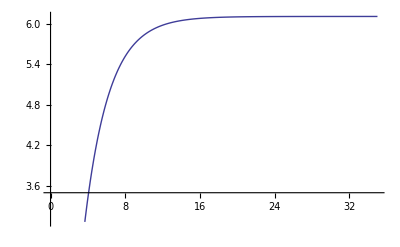

```mathematica
FA=Plot[m(1-2 Exp[-x/t])/.FFA,{x,0,35}]
```

```mathematica
Show[FA,AP]
```

Show::gcomb: Could not combine the graphics objects in GraphicsBox[List[List[List[], List[], List[Hue[0.67`, 0.6`, 0.6`], LineBox[List[List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], Skeleton[521]]]]]], List[Rule[AspectRatio, NCache[Power[GoldenRatio, -1], 0.6180339887498948`]], Rule[Axes, True], Rule[AxesOrigin, List[0, 3.5`]], Rule[PlotRange, List[List[0, 35], List[3.068777107661337`, 6.105584997793872`]]], Rule[PlotRangeClipping, True], Rule[PlotRangePadding, List[Scaled[0.02`], Scaled[0.02`]]]]], AP.

Show[-Graphics-,AP]

```mathematica
B=Transpose[{{2.8825,4.921,7.220,7.807,8.86,9.927,20.934,33.112},{3.10,3.99,4.88,4.93,5.2,5.29,6.16,6.31}}]
```

{{2.8825,3.1},{4.921,3.99},{7.22,4.88},{7.807,4.93},{8.86,5.2},{9.927,5.29},{20.934,6.16},{33.112,6.31}}

```mathematica
Export["C:\\SRE02.dat",Transpose[Append[Transpose[B],Table[0.05,{i,Length[B]}]]]]
```

C:\SRE02.dat

```mathematica
Export["C:\\SRE02b.dat",Transpose[Join[Transpose[B],{Table[0.05,{i,Length[B]}],Table[0.05,{i,Length[B]}]}]]]
```

C:\SRE02b.dat

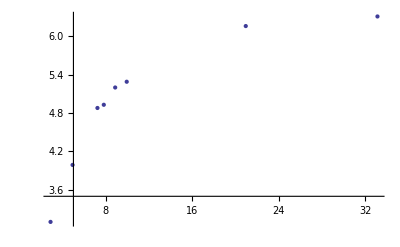

```mathematica
BP=ListPlot[B]
```

```mathematica
NonlinearRegress[B,m(1- Exp[-x/t]),{m,t},x]
```

{BestFitParameters→{m→6.20275,t→4.71361},ParameterCITable→ | Estimate | Asymptotic SE | CI
m | 6.20275 | 0.100366 | {5.95717,6.44834}
t | 4.71361 | 0.226975 | {4.15822,5.269},EstimatedVariance→0.0199299,ANOVATable→ | DF | SumOfSq | MeanSq
Model | 2 | 206.316 | 103.158
Error | 6 | 0.119579 | 0.0199299
Uncorrected Total | 8 | 206.435 | 
Corrected Total | 7 | 7.83275 | ,AsymptoticCorrelationMatrix→(1. | 0.794386
0.794386 | 1.),FitCurvatureTable→ | Curvature
Max Intrinsic | 0.0467384
Max Parameter-Effects | 0.0393828
95. % Confidence Region | 0.440942}

```mathematica
4.7136-4.158221509069886
```

0.555378

```mathematica
FFB=FindFit[B,{m(1- Exp[-x/t]),{0≤m<=10,0≤t≤50}},{m,t},x]
```

FindFit::eit: The algorithm does not converge to the tolerance of 4.80622×10^-6 in 500 iterations. The best estimated solution, with feasibility residual, KKT residual or complementary residual of {0.0000445421, 3.0439×10^-6, 0.0000153363}, is returned.

{m→6.20269,t→4.71348}

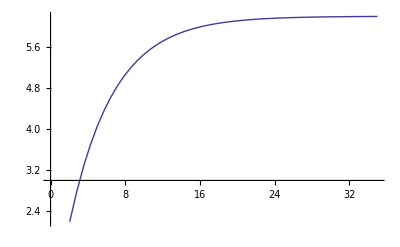

```mathematica
FB=Plot[m(1- Exp[-x/t])/.FFB,{x,0,35}]
```

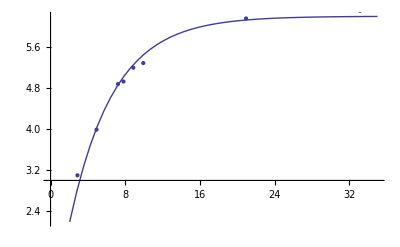

```mathematica
Show[FB,BP]
```

```mathematica
F= Transpose[{0.5{2.022,2.84,4.3,6.985,8.713,12.098},{4.29,3.11,2.65,1.57,1.15,0.63}}]
```

{{1.011,4.29},{1.42,3.11},{2.15,2.65},{3.4925,1.57},{4.3565,1.15},{6.049,0.63}}

```mathematica
Export["C:\\SPE02.dat",Transpose[Append[Transpose[F],Table[0.05,{i,Length[F]}]]]]
```

C:\SPE02.dat

```mathematica
Export["C:\\SPE02b.dat",Transpose[Join[Transpose[F],{Table[0.05,{i,Length[F]}],Table[0.05,{i,Length[F]}]}]]]
```

C:\SPE02b.dat

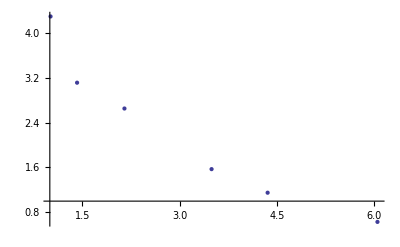

```mathematica
FP=ListPlot[F]
```

```mathematica
FFF=FindFit[F,{m( Exp[-2x/t]),{0≤m<=10,0≤t≤50}},{m,t},x]
```

{m→5.9801,t→5.17891}

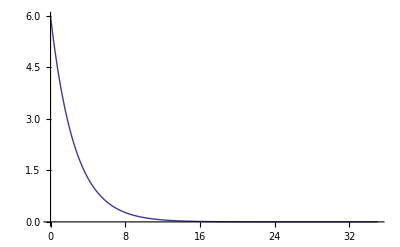

```mathematica
FF=Plot[m(Exp[-2x/t])/.FFF,{x,0,35},PlotRange-> Full]
```

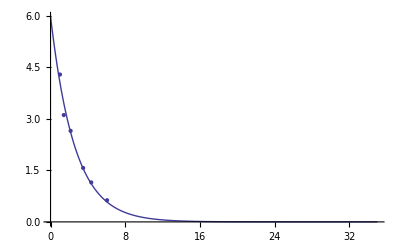

```mathematica
Show[FF,FP]
```

```mathematica
G=Transpose[{0.5 {5.553,3.635,10.686,14.576,18.98,25.62,37.46,45.33,52.4,60.15},{3.695,4.19,2.893,2.379,1.877,1.327,0.71,0.446,0.299,0.203}}]
```

{{2.7765,3.695},{1.8175,4.19},{5.343,2.893},{7.288,2.379},{9.49,1.877},{12.81,1.327},{18.73,0.71},{22.665,0.446},{26.2,0.299},{30.075,0.203}}

```mathematica
Export["C:\\SPE0x.dat",Transpose[Append[Transpose[G],Table[0.05,{i,Length[G]}]]]]
```

C:\SPE0x.dat

```mathematica
Export["C:\\SPE0xb.dat",Transpose[Join[Transpose[G],{Table[0.05,{i,Length[G]}],Table[0.05,{i,Length[G]}]}]]]
```

C:\SPE0xb.dat

```mathematica
NonlinearRegress[P,m Exp[-2x/t],{m,t},x]
```

{BestFitParameters→{m→2.11027,t→226.629},ParameterCITable→ | Estimate | Asymptotic SE | CI
m | 2.11027 | 0.0526347 | {1.96414,2.25641}
t | 226.629 | 26.9216 | {151.883,301.375},EstimatedVariance→0.00826723,ANOVATable→ | DF | SumOfSq | MeanSq
Model | 2 | 19.5932 | 9.79662
Error | 4 | 0.0330689 | 0.00826723
Uncorrected Total | 6 | 19.6263 | 
Corrected Total | 5 | 0.797027 | ,AsymptoticCorrelationMatrix→(1. | -0.567234
-0.567234 | 1.),FitCurvatureTable→ | Curvature
Max Intrinsic | 0.0175911
Max Parameter-Effects | 0.362073
95. % Confidence Region | 0.379478}

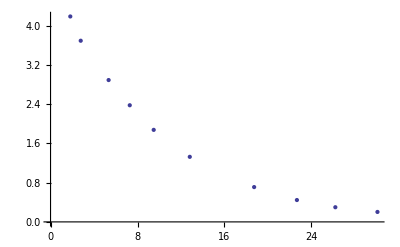

```mathematica
GP=ListPlot[G]
```

```mathematica
FFG=FindFit[G,{m( Exp[-2x/t]),{0≤m<=10,0≤t≤50}},{m,t},x]
```

{m→5.0274,t→19.1526}

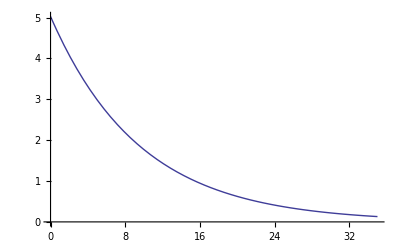

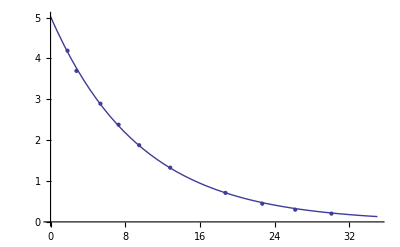

```mathematica
Show[GP,Plot[m( Exp[-2x/t])/.FFG,{x,0,35}]]
```

```mathematica
H=Transpose[{{2.418,6.375,10.092,13.977,27.47,64.65},{2.17,2.79,3.19,3.65,4.581,5.74}}]
```

{{2.418,2.17},{6.375,2.79},{10.092,3.19},{13.977,3.65},{27.47,4.581},{64.65,5.74}}

```mathematica
Export["C:\\SRE0x.dat",Transpose[Append[Transpose[H],Table[0.05,{i,Length[H]}]]]]
```

C:\SRE0x.dat

```mathematica
Export["C:\\SRE0xb.dat",Transpose[Join[Transpose[H],{Table[0.05,{i,Length[H]}],Table[0.05,{i,Length[H]}]}]]]
```

C:\SRE0xb.dat

```mathematica
NonlinearRegress[P,m Exp[-2x/t],{m,t},x]
```

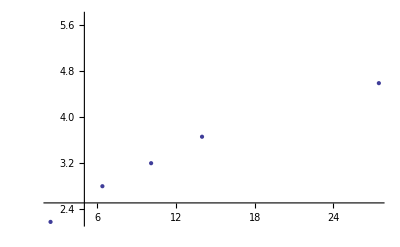

```mathematica
HP=ListPlot[H]
```

```mathematica
NonlinearRegress[H,m(1- Exp[-x/t]),{m,t},x]
```

{BestFitParameters→{m→5.27226,t→9.63544},ParameterCITable→ | Estimate | Asymptotic SE | CI
m | 5.27226 | 0.535786 | {3.78468,6.75984}
t | 9.63544 | 2.65335 | {2.26856,17.0023},EstimatedVariance→0.408519,ANOVATable→ | DF | SumOfSq | MeanSq
Model | 2 | 88.2907 | 44.1453
Error | 4 | 1.63408 | 0.408519
Uncorrected Total | 6 | 89.9248 | 
Corrected Total | 5 | 8.36832 | ,AsymptoticCorrelationMatrix→(1. | 0.742946
0.742946 | 1.),FitCurvatureTable→ | Curvature
Max Intrinsic | 0.26555
Max Parameter-Effects | 0.335222
95. % Confidence Region | 0.379478}

```mathematica
9.635440000097441-2.2685636900144095
```

7.36688

```mathematica
FFH=FindFit[H,{m(1- Exp[-x/t])},{m,t},x]
```

{m→5.27226,t→9.63544}

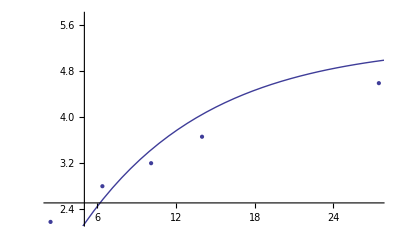

```mathematica
Show[HP,Plot[m(1- Exp[-x/t])/.FFH,{x,0,35},PlotRange-> Full]]
```

```mathematica
J=Transpose[{{19.762,26.381,22.453,37.537,33.946,30.25,43.47,55.43,89.45},{1.78,2.80,2.19,3.92,3.62,3.24,4.51,5.06,5.73}}]
```

{{19.762,1.78},{26.381,2.8},{22.453,2.19},{37.537,3.92},{33.946,3.62},{30.25,3.24},{43.47,4.51},{55.43,5.06},{89.45,5.73}}

```mathematica
Export["C:\\IRE0x.dat",Transpose[Append[Transpose[J],Table[0.05,{i,Length[J]}]]]]
```

C:\IRE0x.dat

```mathematica
Export["C:\\IRE0xb.dat",Transpose[Join[Transpose[J],{Table[0.05,{i,Length[J]}],Table[0.05,{i,Length[J]}]}]]]
```

C:\IRE0xb.dat

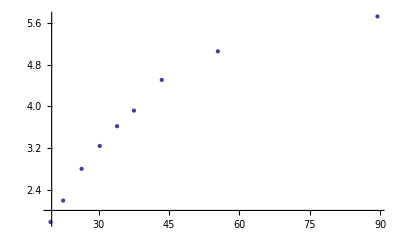

```mathematica
JP=ListPlot[J]
```

```mathematica
FFJ=FindFit[J,{m(1-2 Exp[-x/t]),{0≤m<=10,0≤t≤50}},{m,t},x]
```

{m→5.70446,t→19.3354}

```mathematica
NonlinearRegress[J,m(1-2 Exp[-x/t]),{m,t},x]
```

{BestFitParameters→{m→5.70454,t→19.3357},ParameterCITable→ | Estimate | Asymptotic SE | CI
m | 5.70454 | 0.092729 | {5.48527,5.92381}
t | 19.3357 | 0.36729 | {18.4672,20.2042},EstimatedVariance→0.0136681,ANOVATable→ | DF | SumOfSq | MeanSq
Model | 2 | 133.454 | 66.7269
Error | 7 | 0.095677 | 0.0136681
Uncorrected Total | 9 | 133.55 | 
Corrected Total | 8 | 13.647 | ,AsymptoticCorrelationMatrix→(1. | 0.782557
0.782557 | 1.),FitCurvatureTable→ | Curvature
Max Intrinsic | 0.00920316
Max Parameter-Effects | 0.0508245
95. % Confidence Region | 0.459441}

```mathematica
(19.335671403814917-18.467168377086722)
```

0.868503

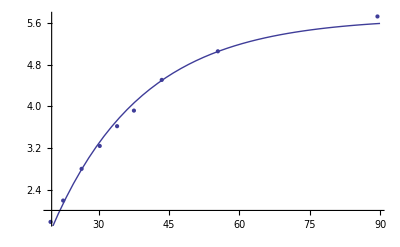

```mathematica
Show[JP,Plot[m(1-2 Exp[-x/t])/.FFJ,{x,10,90},PlotRange-> Full]]
```

```mathematica
K=Transpose[{{6.072,9.047,7.693,10.995,12.988,14.955,20.28,31.318,66.19},{0.62,1.82,1.22,2.45,3.045,3.44,4.40,5.33,5.91}}]
```

{{6.072,0.62},{9.047,1.82},{7.693,1.22},{10.995,2.45},{12.988,3.045},{14.955,3.44},{20.28,4.4},{31.318,5.33},{66.19,5.91}}

```mathematica
Export["C:\\IRE01.dat",Transpose[Append[Transpose[K],Table[0.05,{i,Length[K]}]]]]
```

C:\IRE01.dat

```mathematica
Export["C:\\IRE01b.dat",Transpose[Join[Transpose[K],{Table[0.05,{i,Length[K]}],Table[0.05,{i,Length[K]}]}]]]
```

C:\IRE01b.dat

```mathematica
NonlinearRegress[K,m(1-2 Exp[-x/t]),{m,t},x, ConfidenceLevel->.6827]
```

{BestFitParameters→{m→5.54784,t→8.36},ParameterCITable→ | Estimate | Asymptotic SE | CI
m | 5.54784 | 0.168287 | {5.36664,5.72904}
t | 8.36 | 0.279064 | {8.05952,8.66048},EstimatedVariance→0.0670196,ANOVATable→ | DF | SumOfSq | MeanSq
Model | 2 | 114.521 | 57.2606
Error | 7 | 0.469137 | 0.0670196
Uncorrected Total | 9 | 114.99 | 
Corrected Total | 8 | 26.4109 | ,AsymptoticCorrelationMatrix→(1. | 0.603315
0.603315 | 1.),FitCurvatureTable→ | Curvature
Max Intrinsic | 0.0197504
Max Parameter-Effects | 0.0577719
68.27 % Confidence Region | 0.857956}

```mathematica
(5.729043614424136-5.547842876536437)
```

0.181201

ListPlot[K]

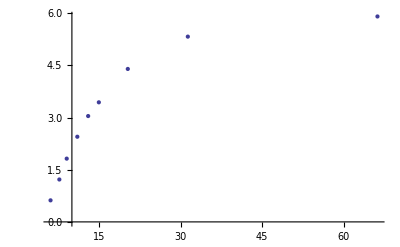

```mathematica
KP=ListPlot[K]
```

```mathematica
FFK=FindFit[K,{m(1-2 Exp[-x/t]),{0≤m<=10,0≤t≤50}},{m,t},x]
```

FindFit::eit: The algorithm does not converge to the tolerance of 4.80622×10^-6 in 500 iterations. The best estimated solution, with feasibility residual, KKT residual or complementary residual of {0.0000200426, 6.72046×10^-7, 9.65822×10^-6}, is returned.

{m→5.5478,t→8.35994}

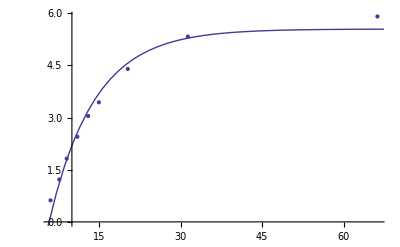

```mathematica
Show[KP,FK=Plot[m(1-2 Exp[-x/t])/.FFK,{x,0,70},PlotRange-> Full]]
```

```mathematica
L=Transpose[{{1.6793,3.3312,4.733,7.663,11.862,18.981,50.17},{2.56,2.83,3.21,3.83,4.43,5.09,5.87}}]
```

{{1.6793,2.56},{3.3312,2.83},{4.733,3.21},{7.663,3.83},{11.862,4.43},{18.981,5.09},{50.17,5.87}}

```mathematica
Export["C:\\SRE01.dat",Transpose[Append[Transpose[L],Table[0.05,{i,Length[L]}]]]]
```

C:\SRE01.dat

```mathematica
Export["C:\\SRE01b.dat",Transpose[Join[Transpose[L],{Table[0.05,{i,Length[L]}],Table[0.05,{i,Length[L]}]}]]]
```

C:\SRE01b.dat

```mathematica
NonlinearRegress[L,m(1- Exp[-x/t]),{m,t},x]
```

{BestFitParameters→{m→5.28091,t→4.66211},ParameterCITable→ | Estimate | Asymptotic SE | CI
m | 5.28091 | 0.403659 | {4.24327,6.31855}
t | 4.66211 | 1.07257 | {1.90498,7.41924},EstimatedVariance→0.340451,ANOVATable→ | DF | SumOfSq | MeanSq
Model | 2 | 117.823 | 58.9116
Error | 5 | 1.70226 | 0.340451
Uncorrected Total | 7 | 119.525 | 
Corrected Total | 6 | 8.96077 | ,AsymptoticCorrelationMatrix→(1. | 0.710949
0.710949 | 1.),FitCurvatureTable→ | Curvature
Max Intrinsic | 0.238802
Max Parameter-Effects | 0.285512
95. % Confidence Region | 0.415725}

```mathematica
4.662109482596877-7.419237638723131
```

-2.75713

```mathematica
FFL=FindFit[L,{m(1- Exp[-x/t]),{0≤m<=10,0≤t≤50}},{m,t},x]
```

FindFit::eit: The algorithm does not converge to the tolerance of 4.80622×10^-6 in 500 iterations. The best estimated solution, with feasibility residual, KKT residual or complementary residual of {0.0000106627, 6.85956×10^-7, 4.71544×10^-6}, is returned.

{m→5.28086,t→4.66199}

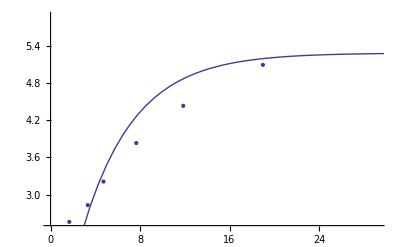

```mathematica
Show[ListPlot[L],Plot[m(1- Exp[-x/t])/.FFL,{x,0,35},PlotRange->Full]]
```

```mathematica
M= Transpose[{0.5{4.881,6.488,9.148,10.897,14.265,17.384,22.153,32.521},{3.03,2.66,2.09,1.85,1.35,0.99,0.622,0.209}}]
```

{{2.4405,3.03},{3.244,2.66},{4.574,2.09},{5.4485,1.85},{7.1325,1.35},{8.692,0.99},{11.0765,0.622},{16.2605,0.209}}

```mathematica
Export["C:\\SPE01.dat",Transpose[Append[Transpose[M],Table[0.05,{i,Length[M]}]]]]
```

C:\SPE01.dat

```mathematica
NonlinearRegress[M,m Exp[-2x/t],{m,t},x]
```

{BestFitParameters→{m→4.73241,t→11.2133},ParameterCITable→ | Estimate | Asymptotic SE | CI
m | 4.73241 | 0.0809246 | {4.5344,4.93043}
t | 11.2133 | 0.238696 | {10.6293,11.7974},EstimatedVariance→0.00153012,ANOVATable→ | DF | SumOfSq | MeanSq
Model | 2 | 27.2711 | 13.6355
Error | 6 | 0.00918072 | 0.00153012
Uncorrected Total | 8 | 27.2803 | 
Corrected Total | 7 | 6.79706 | ,AsymptoticCorrelationMatrix→(1. | -0.898956
-0.898956 | 1.),FitCurvatureTable→ | Curvature
Max Intrinsic | 0.0195123
Max Parameter-Effects | 0.166056
95. % Confidence Region | 0.440942}

```mathematica
4.732412905944776-4.93042836355717
```

-0.198015

```mathematica
Export["C:\\SPE01b.dat",Transpose[Join[Transpose[M],{Table[0.05,{i,Length[M]}],Table[0.05,{i,Length[M]}]}]]]
```

C:\SPE01b.dat

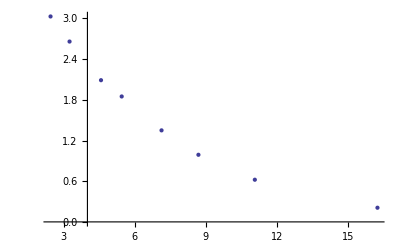

```mathematica
MP=ListPlot[M]
```

```mathematica
FFM=FindFit[M,{m( Exp[-2x/t]),{0≤m<=10,0≤t≤50}},{m,t},x]
```

{m→4.73239,t→11.2134}

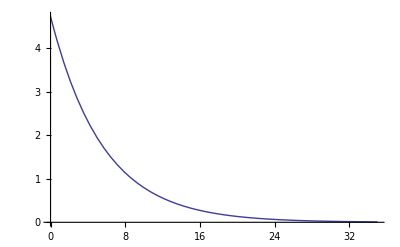

```mathematica
FM=Plot[m( Exp[-2x/t])/.FFM,{x,0,35},PlotRange->Full]
```

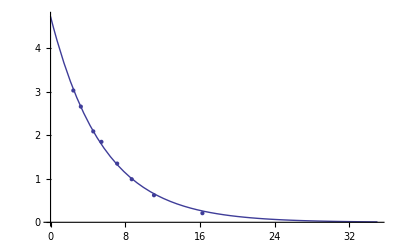

```mathematica
Show[FM,MP]
```

```mathematica
P= Transpose[{0.5{3.542,4.716,8.461,25.31,98.75,127.33},{2.12,2.000,1.975,1.974,1.45,1.11}}]
```

{{1.771,2.12},{2.358,2.},{4.2305,1.975},{12.655,1.974},{49.375,1.45},{63.665,1.11}}

```mathematica
Export["C:\\SPE0w.dat",Transpose[Append[Transpose[P],Table[0.05,{i,Length[P]}]]]]
```

C:\SPE0w.dat

```mathematica
Export["C:\\SPE0wb.dat",Transpose[Join[Transpose[P],{Table[0.05,{i,Length[P]}],Table[0.05,{i,Length[P]}]}]]]
```

C:\SPE0wb.dat

```mathematica
NonlinearRegress[P,m Exp[-2x/t],{m,t},x]
```

{BestFitParameters→{m→2.11027,t→226.629},ParameterCITable→ | Estimate | Asymptotic SE | CI
m | 2.11027 | 0.0526347 | {1.96414,2.25641}
t | 226.629 | 26.9216 | {151.883,301.375},EstimatedVariance→0.00826723,ANOVATable→ | DF | SumOfSq | MeanSq
Model | 2 | 19.5932 | 9.79662
Error | 4 | 0.0330689 | 0.00826723
Uncorrected Total | 6 | 19.6263 | 
Corrected Total | 5 | 0.797027 | ,AsymptoticCorrelationMatrix→(1. | -0.567234
-0.567234 | 1.),FitCurvatureTable→ | Curvature
Max Intrinsic | 0.0175911
Max Parameter-Effects | 0.362073
95. % Confidence Region | 0.379478}

```mathematica
226.62896607256073-301.3752393589258
```

-74.7463

```mathematica
FFP=FindFit[P,{m( Exp[-2x/t]),{0≤m<=10}},{m,t},x]
```

{m→2.11027,t→226.63}

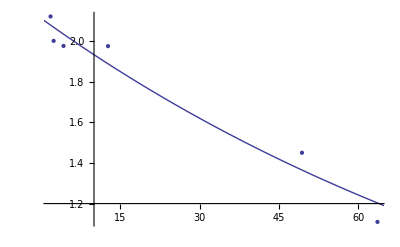

```mathematica
Show[ListPlot[P,PlotRange->Full],Plot[m( Exp[-2x/t])/.FFP,{x,0,70},PlotRange-> Full]]
```